```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
dates=Select[allDates,StringStartsQ[#,{"2017"}]&];
counts:=Counts[dates];
days:=365;
```

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]];
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
{n,categories}
```

{8,<|0→23,1→67,2→86,3→87,4→53,5→28,6→16,7→1,8→4|>}

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{987/365,2.70411}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0669299,0.180986,0.244703,0.220568,0.14911,0.0806418,0.0363441,0.0140398,0.00667868},{24.4294,66.0598,89.3165,80.5072,54.4251,29.4343,13.2656,5.12451,2.43772}}

```mathematica
observe=Values[categories]
```

{23,67,86,87,53,28,16,1,4}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

5.73553

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.766068

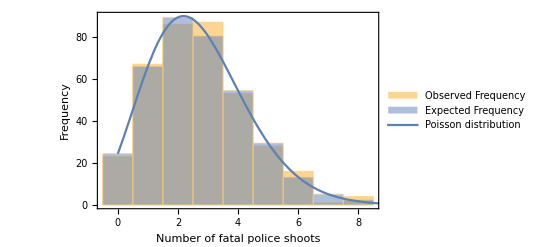

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+1},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q3-2017-exp.eps",fig];
```